# POE Lab 2 - 3D Scanner

## Voltage to Distance

```mathematica
distanceCSV=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Csv"];
distanceData=distanceCSV[[2;;Length[distanceCSV]-1]];
```

```mathematica
Fit[Map[Reverse,distanceData], {1,x,x^2,x^3},x]
```

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

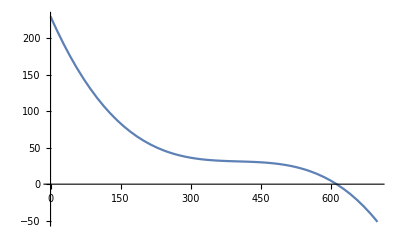

```mathematica
Plot[230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3,{x,0,700}]
```

## Test Calibration

```mathematica
groundTruth={17,27,37,47,67,87};
measuredVoltage={571,462,353,288,199,162};
measuredDistance=voltageToDistance/@measuredVoltage;
```

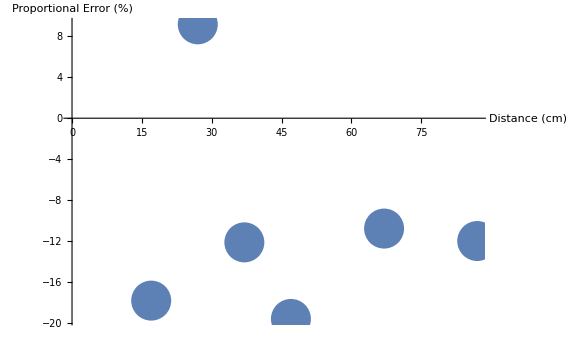

```mathematica
ListPlot[Transpose@{groundTruth,(measuredDistance-groundTruth)/groundTruth*100},AxesLabel->{"Distance (cm)","Proportional Error (%)"},PlotStyle->PointSize[.05],ImageSize->Large,PlotRange->{{0,Automatic},{Automatic,Automatic}}]
```

## Make Functions

```mathematica
voltageToDistance[x_]=(230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3);
anglesToPan[servo1_,servo2_]:=Module[{},(N@servo1-servo2)/2]
anglesToTilt[servo1_,servo2_]:=Module[{},(N@servo1+servo2)/2]
```

```mathematica
panTiltDistance[{servo1_,servo2_,voltage_}]:=Module[{pan,tilt,distance},
pan=anglesToPan[servo1,servo2];
tilt=anglesToTilt[servo1,servo2];
distance=voltageToDistance[voltage];
Return[{distance,tilt,pan}]
]
```

```mathematica
ClearAll@toCartesian;
toCartesian[{distance_,tilt_,pan_}]:=Module[{radPan,radTilt,basePoint,panRotation,tiltRotation},
radPan=pan*π/180;
radTilt=tilt*π/180;
basePoint=distance*{1,0,0};
panRotation=RotationMatrix[radPan,{0,0,1}];
tiltRotation=RotationMatrix[radTilt,{0,1,0}];
tiltRotation.panRotation.basePoint
]
```